# 2014年北京公共汽车需求曲线分析

基础学科试点班 数学与应用数学（交通系统科学方向）

小组成员：辛嘉琪19221261；赵宏瑞19251140；董一飞19271036；

2021年3月

## 分析对象：

2014年北京公共汽车的需求、供给曲线影响因素以及相关弹性分析。
-Graphics-

公共汽车（BUS）属于道路公共交通的一种，是保障大多数人出行的高效、低碳、绿色、环保的一种出行方式。

具备排他性，但具有一定程度的消费非竞争性，视作"准公共物品"。具有显著的正外部性。

供给方式：
	• 政府主导投资：政府直接提供。
	• 国有运营：在政府给予补贴的条件下，由私人企业提供。
	• 线路专营：不同线路，不同区域，可以存在不同的公交企业
	• 多元化、市场化，具有一定的垄断性质
“北京公共交通控股（集团）有限公司”是北京地面公共交通的经营主体。（特大型国有独资企业）

## 北京地面公交系统需求曲线

2014年，有学者针对北京地面公交系统，计算出了不同票价水平下公交客流量^[1]。考虑票价制定的习惯，计算中票价每次调整的幅度为0.5元，政府限定最高票价为5元。

```mathematica
ticketprice=Range[1,5,0.5];
passengerflow={217782,196481,171001,142910,114480,87998,65117,46596,32403};
data=Table[{passengerflow[[i]],ticketprice[[i]]},{i,1,9}];
Grid[{{"公交车票价（元）",1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.},{"客流量（人/日）",217782,196481,171001,142910,114480,87998,65117,46596,32403}},Frame->All,ItemSize->{9,3}]
```

公交车票价（元） | 1. | 1.5 | 2. | 2.5 | 3. | 3.5 | 4. | 4.5 | 5.
客流量（人/日） | 217782 | 196481 | 171001 | 142910 | 114480 | 87998 | 65117 | 46596 | 32403

图表：

```mathematica
A1 = ListPlot[{data->passengerflow},LabelingFunction->Above,PlotLabel->"图1：2014年北京公交车票价与客流量曲线",
AxesLabel->{"客流量（人/日）","公交车票价（元）"},PlotRange->{{10000,250000},{0.5,5.5}},ImageSize->Large,Joined->True,Mesh->All];
A = ListPlot[{data->passengerflow,Style[{{171001,2}},Red,PointSize[.025]]},LabelingFunction->Above,PlotLabel->"图1：2014年北京公交车票价与客流量曲线",
AxesLabel->{"客流量（人/日）","公交车票价（元）"},PlotRange->{{10000,250000},{0.5,5.5}},ImageSize->Large,Joined->True,Mesh->All];
G = ListPlot[{data->passengerflow,Style[{{114480,3}},Red,PointSize[.025]]},LabelingFunction->Above,PlotLabel->"图2：2014年北京公交车票价与客流量曲线",
AxesLabel->{"客流量（人/日）","公交车票价（元）"},PlotRange->{{10000,250000},{0.5,5.5}},ImageSize->Large,Joined->True,Mesh->All];
G1 = ListPlot[{data->passengerflow,Style[{{65117,4}},Red,PointSize[.025]]},LabelingFunction->Above,PlotLabel->"图2：2014年北京公交车票价与客流量曲线",
AxesLabel->{"客流量（人/日）","公交车票价（元）"},PlotRange->{{10000,250000},{0.5,5.5}},ImageSize->Large,Joined->True,Mesh->All];
Q = Manipulate[Which[k==2,Show[A],k==3,Show[G],k==4,Show[G1]],{{k,2,"公交票价:"},2,4,1,RadioButton}];
Grid[{{A1,Q}}]
```

-Graphics- |

上述图表反映出需求法则：价格与需求呈负相关。反映在需求曲线上，即需求曲线是倾斜向下的。

根据该学者的计算,北京市公交车票价为2元时，需求数量（客流量）为171001人/日；而当票价上涨至3元时，需求数量减少到114480人/日。

## 需求曲线右移：2014年12月28日北京地铁涨价

北京地铁票价由原先的2元调整为：6公里(含)内3元；6-12公里(含)4元；12-22公里(含)5元；22-32公里(含)6元。
  		 -Graphics--Graphics-

此后，学者重新计算了不同票价水平下公交客流量

```mathematica
ticketprice=Range[1,5,0.5];
passengerflowNew={222973,202791,181263,148028,121832,95127,75061,53994,39352};
dataNew=Table[{passengerflowNew[[i]],ticketprice[[i]]},{i,1,9}];
Grid[{{"公交车票价（元）",1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.},{"客流量（人/日）",222973,202791,181263,148028,121832,95127,75061,53994,39352}},Frame->All,ItemSize->{9,3}]
```

公交车票价（元） | 1. | 1.5 | 2. | 2.5 | 3. | 3.5 | 4. | 4.5 | 5.
客流量（人/日） | 222973 | 202791 | 181263 | 148028 | 121832 | 95127 | 75061 | 53994 | 39352

图表：

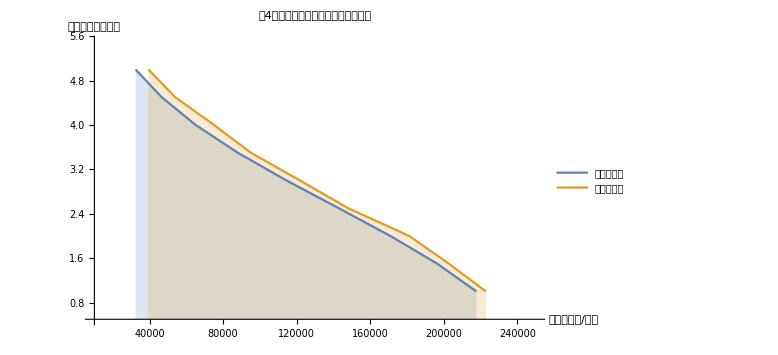
-Graphics- | -Graphics-

```mathematica
B = ListPlot[dataNew->passengerflowNew,LabelingFunction->Above,PlotLabel->"图3：地铁涨价后北京公交车票价与客流量曲线",
AxesLabel->{"客流量（人/日）","公交车票价（元）"},PlotRange->{{10000,250000},{0.5,5.5}},ImageSize->Large,Joined->True,Mesh->All];
F = ListPlot[{data,dataNew},PlotLegends->{"地铁涨价前","地铁涨价后"},PlotRange->{{10000,250000},{0.5,5.5}},
AxesLabel->{"客流量（人/日）","公交车票价（元）"},PlotLabel->"图4：涨价前后北京公交需求曲线变化",Joined->{True,True},Filling->Bottom,ImageSize->Large];
Grid[{{B,F}}]
```

地铁是公交的替代品，当北京市出台新政策，地铁涨价，那么选择公交出行方式的人增加，需求曲线右移。

## 北京公交需求影响因素综合分析

#### 根据表格数据进行线性拟合，得到需求函数：

```mathematica
H = LinearModelFit[data,x,x];
Normal[H]
```

5.44092-0.00002044 x

#### 影响需求曲线的其他因素：

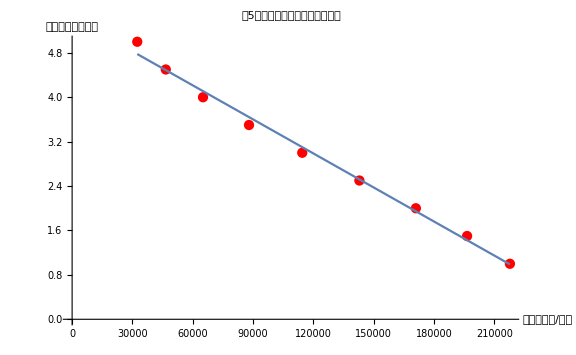
-Graphics- |

```mathematica
J = Show[ListPlot[data,PlotStyle->Red],Plot[%%[x],{x,32403,217782}],ImageSize->Large,
AxesLabel->{"客流量（人/日）","公交车票价（元）"},PlotLabel->"图5：根据表格数据拟合线性曲线"];
L = Manipulate[
Plot[{5.44-0.00002044x,5.44-0.00002044 x+(subway-3)/4-(everageincome-3.5)/4+2(population-2)+adjustment/4+adjustmen/6},{x,-10000,417782},PlotRange->{{0,250000},{0,6}},AxesLabel->{"客流量（人/日）","公交车票价（元）"},
PlotLabel->"图6：北京公交需求影响因素综合分析",
ImageSize->{500,300},PlotLegends->{"原需求曲线","改变后需求曲线"}
],
{{subway,3,"地铁票价（元）"},1,5,0.2,Appearance->"Labeled"},
{{adjustment,0,"对地铁拥挤状况的调整:   
     （公交专用道等）"},{0->"调整前",2->"调整后"}},Delimiter,
{{everageincome,3.5,"人均收入(万元/年）"},2,7,0.2,Appearance->"Labeled"},
{{population,2,"北京市人口（千万人）"},1.8,2.2,0.01,Appearance->"Labeled"},
{{adjustmen,0,"“绿色出行”理念的提倡:   "},{0->"倡导前",2->"倡导后"}}
];
Grid[{{J,L}}]
```

随着北京市人均收入的增加，公交需求曲线左移。这意味着公交出行方式相对属于"劣等商品"的范畴，其需求收入弹性小于零。

由图表可知，北京市人口增加，意味着消费者数量增加，对公交的需求增加，需求曲线右移。

如果社会开始崇尚绿色出行，随着人们消费偏好的改变，公交需求曲线应当会左移。

## 北京公交需求曲线弹性分析

弹性计算公式：η=(ΔQ_d/Q_d)/(ΔP/P)，可由点弹性、弧弹性两种方法计算：

弧弹性由中点公式计算：η=(ΔQ_d/Q_d)/(ΔP/P)=(|Q_d_2-Q_d_1|/1/2(Q_d_1+Q_d_2))/(|P_2-P_1|/1/2(P_1+P_2))=(|Q_d_2-Q_d_1|)/(|P_2-P_1|)·(P_2+P_1)/(Q_d_2+Q_d_1)

点弹性计算公式：η=Limit[(ΔQ_d/Q_d)/(ΔP/P),ΔP→0]= dQ/dP·P/Q

```mathematica
M = Manipulate[If[p1==p2,p1=p2+.01];
Pane[Text@Style[Switch[ type,

1,Grid[{
{Row[{"公式：η=dQ/dP·P/Q"}]},{"\n","\n","\n"},
{Row[{"Δ",Row[{Style["Q_d",Italic]}], " = ",Abs[q1-q2],"     Δ",Row[{Style["P",Italic] }] ," = ",Abs[p1-p2]
}]},
{"\n","\n","\n"},
{Row[{"点弹性  η = ",NumberForm[48923.67624400576 p1/q1,{7,4}]
}]}}],

2,Grid[{
{Row[{"公式：η=(|Q_d_2-Q_d_1|)/(|P_2-P_1|)·(P_2+P_1)/(Q_d_2+Q_d_1)"}]},{"\n","\n","\n"},
{Row[{"Δ",Row[{Style["Q_d",Italic]}]," = ",Abs[q1-q2],"     Δ",Row[{Style["P",Italic]}]," = ",Abs[p1-p2]
}]},{"\n","\n","\n"},
{Row[{"弧弹性  η = ",NumberForm[(Abs[q1-q2]/(.5*(q1+q2)))/(Abs[p1-p2]/(.5*(p1+p2))),{7,4}]}]}}],

3,Grid[{
{Row[{"公式：η_AB=(ΔQ_A/Q_A)/(ΔP_B/P_B)"}]},{"\n","\n"},
{Row[{"Δ",Row[{Style["Q_A",Italic]}]," = ",2.79,"     Δ",Row[{Style["P_B",Italic]}]," = ",1.2
}]},{"\n","\n"},
{Row[{"需求交叉价格弹性  η_AB = ",N[2.79/1.2]}]}}],

4,Grid[{
{Row[{":516c:5f0f:ff1aη_I=(ΔQ/Q)/(ΔI/I)"}]},{"\n","\n"},
{Row[{"Δ",Row[{Style["Q_d",Italic]}]," = ",0.8,"     Δ",Row[{Style["P",Italic]}]," = ",2
}]},{"\n","\n"},
{Row[{"需求收入弹性  η_I = ",-0.400}]}}]

],18],{475,300},Alignment->{Center,Center}],
{{type,1,""},{1->"      点弹性公式      ",2->"      弧弹性公式       "}},

{{p1,2.5,"P_1(元)"},1,5,.01,Appearance->"Labeled"},
{{q1,143881,"Q_d_1（人/日）"},21571.3,217266,1,Appearance->"Labeled"},
{{p2,3,"P_2(元)"},1,5,.01,Appearance->"Labeled"},
{{q2,119419,"Q_d_2（人/日）"},21571.3,217266,1,Appearance->"Labeled"},Delimiter,
{{type,3,""},{3->"地铁公交需求交叉价格弹性",4->"公交需求收入弹性"}}
];Grid[{{J,M}}]
```

-Graphics- |

```mathematica
Solve[5.440917687196457-0.000020440001176782424 x==2,x]
Solve[5.440917687196457-0.000020440001176782424 x==2.5,x]
Solve[5.440917687196457-0.000020440001176782424 x==3,x]
```

{{x→168342.}}

{{x→143881.}}

{{x→119419.}}

当公交车票价为2元左右时，根据点弹性计算公式：

```mathematica
1/0.00002044 2/168342
```

0.581242

知其需求的价格弹性约为0.58。由0.58<1，知公交出行缺乏弹性，对于北京市民而言属于生活必需品，尽管公交出行的费用占市民总支出中比重较小，但仍是一种相对重要的出行方式.

地铁与公交的需求交叉价格弹性为2.325>0,可知二者是替代关系.

北京公交的需求收入弹性为-0.4<0,这意味着公交出行方式相对属于“劣等商品”的范畴.

## 北京公交供给曲线：

公交系统供给量Piecewise[{{基础设施Piecewise[{{运输线路：公路, }, {运输枢纽：车站, }}], }, {运载工具Piecewise[{{公交车数量, }, {公交车载客能力, }}], }}]

在影响公交系统供给量的诸多因素中，票价是最灵敏、最重要的因素。

交通供给函数：Q=f(P)。式中：Q为运输供给量，P为票价。

```mathematica
a= Manipulate[
Plot[{0.00002044x,0.00002044 x+(subway-3)/4+(everageincome-1.5)/1+2(population/4-2)+adjustment/4+adjustmen/6},{x,-10000,417782},PlotRange->{{30000,250000},{0.7,6}},AxesLabel->{"北京公交供给量","公交车票价（元）"},
PlotLabel->"图7：北京公交供给影响因素综合分析",
ImageSize->{500,300},PlotLegends->{"原供给曲线","改变后供给曲线"}
],
{{adjustment,0,":5317:4eac:5e02:653f:5e9c:8d22:653f:8865:507f"},{0->"无(私人产权)",-2->"有(混合产权)"}},
{{adjustmen,0,":6280:672f:521b:65b0 / :4ea7:4e1a:7ed3:6784:8c03:6574"},{0->"前",-2->"后"}},Delimiter,
{{everageincome,1.5,":516c:5171:6c7d:8f66:7ef4:4fee:6210:672c:ff08:767e:4e07:5143:ff09"},1,4/2,0.05,Appearance->"Labeled"},
{{population,2*4,":516c:53f8:7ba1:7406:6210:672c:ff08:767e:4e07:5143:ff09"},1.8*4,2.2*4,0.01,Appearance->"Labeled"},
{{subway,3,":516c:4ea4:7ebf:8def:8fd0:8425:6210:672c:ff08:767e:4e07:5143:ff09"},1,5,0.2,Appearance->"Labeled"}
];
b = Manipulate[If[p1==p2,p1=p2+.01];
Pane[Text@Style[Switch[ type,

1,Grid[{
{Row[{"公式：η=dQ/dP·P/Q"}]},{"\n","\n","\n"},
{Row[{"Δ",Row[{Style["Q_d",Italic]}], " = ",Abs[q1-q2],"     Δ",Row[{Style["P",Italic] }] ," = ",Abs[p1-p2]
}]},
{"\n","\n","\n"},
{Row[{"点弹性  η = ",NumberForm[48923.67624400576 p1/q1,{7,4}]
}]}}],

2,Grid[{
{Row[{"公式：η=(|Q_d_2-Q_d_1|)/(|P_2-P_1|)·(P_2+P_1)/(Q_d_2+Q_d_1)"}]},{"\n","\n","\n"},
{Row[{"Δ",Row[{Style["Q_d",Italic]}]," = ",Abs[q1-q2],"     Δ",Row[{Style["P",Italic]}]," = ",Abs[p1-p2]
}]},{"\n","\n","\n"},
{Row[{"弧弹性  η = ",NumberForm[(Abs[q1-q2]/(.5*(q1+q2)))/(Abs[p1-p2]/(.5*(p1+p2))),{7,4}]}]}}]

],18],{475,300},Alignment->{Center,Center}],
{{type,1,""},{1->"      点弹性公式      ",2->"      弧弹性公式       "}},

{{p1,2.5,"P_1(元)"},1,5,.01,Appearance->"Labeled"},
{{q1,143881,"Q__1(供给量)"},21571.3,217266,1,Appearance->"Labeled"},
{{p2,3,"P_2(元)"},1,5,.01,Appearance->"Labeled"},
{{q2,119419,"Q__2(供给量)"},21571.3,217266,1,Appearance->"Labeled"}];
Grid[{{a,b}}]
```

|

## 参考文献：

#### [1]闫小勇,牛学勤.基于概率选择的城市轨道交通最优票价计算方法[J].学术专论.2003.06:79-82. [2]四兵峰,高自友.城市间公路客运的客票票价与其客流量之间的灵敏度分析[J].中国公路学报,2000,13(02):91-95. [3]陈建华,高自友.多模式条件下需求变动时铁路客票价格制定的优化模型及算法[J].交通运输系统工程与信息,2001,1(4):299-330. [4]尹胜男,李引珍,张长泽.基于客流分配的高铁票价调整策略[J].计算机应用,2020,40(1):278-283. [5]杨德明.城市公交运营成本分析及计算方法研究[D].成都:西南交通大学,2011,2-60.

#### 演示中需求曲线变动与弹性计算的交互式操作改编自WOLFRAM.DEMONSTRATION:

https://demonstrations.wolfram.com/ElasticityAndSlopeWithLinearDemand/

https://demonstrations.wolfram.com/ShiftsInTheDemandCurve/

https://demonstrations.wolfram.com/ThePriceElasticityOfDemand/

-Graphics-Tank you for your listening！